# Spectral Lags in Very High Energy Emission of GRBs

## Numerical functions

### findRoot

Only works for monotonously increasing functions, which have a root for var > 0

```mathematica
findRoot[func_,{var_,start_?NumericQ}]:=Block[{left,right},
If[(func/.var->start)<0,
left=start;
right=2.start;
While[(func/.var->right)<0,right*=2;left*=2];
,
right=start;
left=.5start;
While[(func/.var->left)>0,left*=.5;right*=.5];
];
FindRoot[func,{var,left,right}]
]
```

## Model

### Parameters

```mathematica
universe={Hobs_,Ωm_};
```

```mathematica
population={density0_,index_,zc_};
```

```mathematica
burst={γ_,η0_,r0_,n_,ω0_,θ0_,k_,α_};
```

```mathematica
observer={detectorArea_,z_,χ_};
```

```mathematica
Options[defaultUniverse]={Hobs->2.*^-18,Ωm->0.317};
defaultUniverse[OptionsPattern[]]:={OptionValue[Hobs],OptionValue[Ωm]};
```

```mathematica
Options[defaultPopulation]={density0->0.655427*^-50,index->3,zc->3.};
defaultPopulation[OptionsPattern[]]:={OptionValue[density0],OptionValue[index],OptionValue[zc]};
```

```mathematica
Options[defaultBurst]={γ->300,η0->8.4*^37,r0->1.2*^6,n->22,ω0->1.,θ0->0.000282,k->-0.367,α->-1.280};
defaultBurst[OptionsPattern[]]:={OptionValue[γ],OptionValue[η0],OptionValue[r0],OptionValue[n],OptionValue[ω0],OptionValue[θ0],OptionValue[k],OptionValue[α]};
```

```mathematica
defaultDetectorArea[]:=5.563*^-18;
```

```mathematica
Options[defaultObserver]={detectorArea->defaultDetectorArea[],z->2.1062,χ->0.0113};
defaultObserver[OptionsPattern[]]={OptionValue[detectorArea],OptionValue[z],OptionValue[χ]};
```

### Relativity

```mathematica
v[γ_]:=√(1-1/γ^2);
```

### Cosmology

```mathematica
ΩΛ[Ωm_]:=1-Ωm;
```

```mathematica
distance[universe,z_]:=1/Hobs √(1/ΩΛ[Ωm])((1+z)Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm](1+z)^3]-Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm]]);
```

```mathematica
photonSphereArea[universe_,z_]:=4π distance[universe,z]^2;
```

```mathematica
burstsSphereArea[universe_,z_]:=(4π distance[universe,z]^2)/(1+z)^2;
```

```mathematica
shellVolumePerRedshift[universe,z_]:=(4π distance[{Hobs,Ωm},z]^2)/(1+z)^3 1/(Hobs √(Ωm(1+z)^3+ΩΛ[Ωm]));
```

### Light curve

```mathematica
i[burst,z_,χ_,ω_,θ_,ϕ_]:=
If[ω==∞,
0,
1/(2k)ω(ω/ω0)^α ExpIntegralE[(α+1)/(2k)+1,(θ/θ0)^2(ω/ω0)^(-2k)(v[γ]γ(1+z)(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ]))^(-2k)]
];
```

```mathematica
j[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z))^3 π/(n Sin[(3π)/n]),
τ^3/3 Hypergeometric2F1[1,3/n,(n+3)/n,-(τ/(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z)))^n]
];
```

```mathematica
p[universe_,burst,observer,{θ_,ϕ_},{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
Re[detectorArea/photonSphereArea[universe,z] η0/(v[γ]γ(1+z))^(2-α)1/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ])]
];
```

```mathematica
p[universe_,burst,observer,{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
2/γ^2(NIntegrate[θ p[universe,burstValues,{detectorArea,z,χ},{θ/γ,ϕ},{τ1,τ2},{ω1,ω2}],{θ,0,γ χ},{ϕ,0,π},Method->{"GlobalAdaptive",Method->"GaussKronrodRule"}]+NIntegrate[θ p[universe,burstValues,{detectorArea,z,χ},{θ/γ,ϕ},{τ1,τ2},{ω1,ω2}],{θ,γ χ,∞},{ϕ,0,π},Method->{"GlobalAdaptive",Method->"GaussKronrodRule"}])
]
```

### Duration

```mathematica
Options[duration]={part->0.99};
duration[universe_,burst,observer,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,observerValues,p∞,precision,pi},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
observerValues={detectorArea,z,χ};
p∞=p[universe,burstValues,observerValues,{0.,∞},{ω1,ω2}];
pi[τ_?NumericQ]:=p[universe,burstValues,observerValues,{0.,τ},{ω1,ω2}];
τ/.findRoot[pi[τ]-OptionValue[part]p∞,{τ,r0/γ^2(1.+z)}]
];
```

### Stretching factor

```mathematica
jτ[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
0,
Re[τ^2/(1+((2τ)/(r0 (1+z) (-2+2/v[γ]+θ^2+χ^2-2 θ χ Cos[ϕ])))^n)]
];
```

```mathematica
pτ[universe_,burst,observer,{θ_,ϕ_},τ_,{ω1_,ω2_}]:=Block[{burstValues},
Re[detectorArea/photonSphereArea[universe,z] η0/(v[γ]γ(1+z))^(2-α)1/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ]]
]
```

```mathematica
pτ[universe_,burst,observer,τ_,{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
2/γ^2(NIntegrate[θ pτ[universe,burstValues,{detectorArea,z,χ},{θ/γ,ϕ},τ,{ω1,ω2}],{θ,0,γ χ},{ϕ,0,π}]+NIntegrate[θ pτ[universe,burstValues,{detectorArea,z,χ},{θ/γ,ϕ},τ,{ω1,ω2}],{θ,γ χ,∞},{ϕ,0,π}])
]
```

```mathematica
Options[κ]={δ->0.01,accurateQ->True};
κ[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{p12∞,p23∞,diff,diffτ,δτ,τmiddle,τend,κmin,κmax,minDifference,maxDifference,diffDifference,precision,accQ},
p12∞=p[universe,burst,observer,{0.,∞},{ω1,ω2}];
p23∞=p[universe,burst,observer,{0.,∞},{ω2,ω3}];
diff[τ_?NumberQ,κ_?NumberQ]:=p[universe,burst,observer,{0.,τ},{ω1,ω2}]/(p12∞)-p[universe,burst,observer,{0.,κ τ},{ω2,ω3}]/(p23∞);
diffτ[τ_?NumberQ,κ_?NumberQ]:=pτ[universe,burst,observer,τ,{ω1,ω2}]/(p12∞)-κ pτ[universe,burst,observer,κ τ,{ω2,ω3}]/(p23∞);
accQ=OptionValue[accurateQ];
If[TrueQ[accQ],
τend=duration[universe,burst,observer,{ω1,ω3}];
δτ=OptionValue[δ]τend;
maxDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]>0,
If[diff[τend,κ]>0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,zero-δτ}];
];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
];
minDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]<0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
If[diff[τend,κ]<0,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,zero+δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
]
];
κmax=κi/.findRoot[-diff[δτ,κi],{κi,1.}];
κmin=κi/.findRoot[-diff[τend,κi],{κi,1.}];
diffDifference[κ_?NumberQ]:=maxDifference[κ][[2]]+minDifference[κ][[2]];
κi/.FindRoot[diffDifference[κi],{κi,κmin,κmax}]
,
τmiddle=duration[universe,burst,observer,{ω1,ω3},part->0.5];
κi/.findRoot[-diff[τmiddle,κi],{κi,1.}]
]
];
```

```mathematica
SetSharedFunction[κStoredValues];
Options[κCache]={δ->0.01,accurateQ->True};
κCache[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{},
If[Not[NumberQ[κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]]],κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]=κ[universe,burst,observer,{ω1,ω2,ω3},δ->OptionValue[δ],accurateQ->OptionValue[accurateQ]]];
κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]
];
```

```mathematica
κSave[]:=DumpSave["kappa.mx",κStoredValues];
```

```mathematica
κLoad[]:=If[FileExistsQ["kappa.mx"],<<"kappa.mx"];
```

### Total Energy

```mathematica
energy[burst,ω1_]:=(16 π^3)/(3n(-2k-α-2)Sin[(3π)/n])γ^(-2k-α)(1-1/(4 γ^2))η0 r0^3 θ0^2 ω0^(-2k-α)/ω1^(-2k-α-2);
```

### Distribution of stretching factors

```mathematica
Options[zmax]={minParticles->10};
zmax[universe_,burst_,detectorArea_,χ_,{ω1_,ω2_},OptionsPattern[]]:=Block[{int,z1,z2},
int[z_?NumericQ]:=p[universe,burst,{detectorArea,z,χ},{0,∞},{ω1,ω2}]-OptionValue[minParticles];
z1=1;
While[int[z1]<0,z1/=2.];
z2=1;
While[int[z2]>0,z2*=2.];
z/.FindRoot[int[z],{z,z1,z2}]
];
```

```mathematica
Options[χmax]={minParticles->10};
χmax[universe_,burst,detectorArea_,z_,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,int,χ0},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
int[χ_?NumberQ]:=p[universe,burstValues,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
If[int[0]<0,
Return[0],
χ0=1/γ;
While[int[χ0]>0,χ0*=2.;];
];
χ/.FindRoot[int[χ],{χ,0,χ0}]
];
```

```mathematica
burstDensity[population,z_]:=density0(1+z)^index Exp[-z/zc];
```

```mathematica
phaseVolume[universe_,population_,{z1_?NumberQ,z2_?NumberQ}]:=NIntegrate[shellVolumePerRedshift[universe,z]burstDensity[population,z],{z,z1,z2}];
```

```mathematica
randomRedshift[universe_,population_,{z1_,z2_}]:=Block[{total,chosenVolume},
total=phaseVolume[universe,population,{z1,z2}];
chosenVolume=RandomReal[total];
z/.FindRoot[phaseVolume[universe,population,{z1,z}]-chosenVolume,{z,z1,z2}]
];
```

```mathematica
randomAngle[{χ1_,χ2_}]:=√RandomReal[{χ1^2,χ2^2}];
```

```mathematica
inRegionQ[region_,point_]:=Block[{i},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]≤point[[1]]&&region[[i]][[2]]≤point[[2]],Return[True]];
];
Return[False];
];
```

```mathematica
addToRegion[region_,point_]:=Block[{i,j},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]>point[[1]],
If[i==1||region[[i-1]][[2]]>point[[2]],
For[j=i,j≤Length[region]&&region[[j]][[2]]>point[[2]],j++];
Return[Insert[Drop[region,{i,j-1}],point,i]];
,
Return[region];
];
];
];
If[Length[region]==0||region[[Length[region]]][[2]]>point[[2]],
Return[Insert[region,point,Length[region]+1]];
,
Return[region];
];
];
```

```mathematica
Options[plotRegion]={axesOrigin->Automatic};
plotRegion[region_,range_,OptionsPattern[]]:=Block[{plotPoints},
If[Length[region]==0,Return[ListPlot[{Missing},PlotRange->range]]];
plotPoints=Flatten[Table[{region[[i]],{region[[i+1]][[1]],region[[i]][[2]]}},{i,1,Length[region]-1}],1];
AppendTo[plotPoints,region[[Length[region]]]];
AppendTo[plotPoints,{range[[1]][[2]],region[[Length[region]]][[2]]}];
ListPlot[plotPoints,PlotStyle->LightRed,Joined->True,PlotRange->range,Filling->Top,FillingStyle->LightRed,AxesOrigin->OptionValue[axesOrigin]]
];
```

```mathematica
burstSample::usage="burstSample computes a sample of properties of uniformly distributed GRBs. Possible values for computedValues are {z, χ, pTotal, pLow, pHigh, duration, κ, κNotAccurate}";
Options[burstSample]={randomSeed->"Gamma Rays",zmin->0.1,computedValues->{"z","χ","pLow","pHigh","duration","κ"},minParticles->10,monitorQ->False};
burstSample[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},n_,OptionsPattern[]]:=Block[{
z2,χ2,it,zc,χc,pointsChosen,startedCount,completedCount,result,pointResult,region,print
},
SeedRandom[OptionValue[randomSeed]];
pointsChosen={};
startedCount=0;
completedCount=0;
SetSharedVariable[completedCount];
SetSharedVariable[startedCount];
region={};
it=0;
If[OptionValue[monitorQ],
print=PrintTemporary[Dynamic[
If[it==0,"initializing",
If[startedCount>0,ToString[completedCount]<>"/"<>ToString[n]<>" κ values computed",
ToString[Length[pointsChosen]]<>"/"<>ToString[n]<>" points chosen"
]
]
]]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
χ2=χmax[universe,burst,detectorArea,OptionValue[zmin],{ω2,ω3},minParticles->OptionValue[minParticles]];
For[it=1,it≤n,it++,
zc=randomRedshift[universe,population,{OptionValue[zmin],z2}];
χc=randomAngle[{0,χ2}];
If[inRegionQ[region,{zc,χc}],it--,
If[p[universe,burst,{detectorArea,zc,χc},{0,∞},{ω2,ω3}]≥10.,
AppendTo[pointsChosen,{zc,χc}];
,
region=addToRegion[region,{zc,χc}];
it--;
];
];
];
κLoad[];
result=ParallelTable[
startedCount++;
pointResult=ReleaseHold[OptionValue[computedValues]/.{
"z"->Hold[point[[1]]],
"χ"->Hold[point[[2]]],
"pTotal"->Hold[p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω1,ω3}]],
"pLow"->Hold[p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω1,ω2}]],
"pHigh"->Hold[p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω2,ω3}]],
"duration"->Hold[duration[universe,burst,Flatten[{detectorArea,point}],{ω1,ω3}]],
"κ"->Hold[κCache[universe,burst,Flatten[{detectorArea,point}],{ω1,ω2,ω3}]],
"κNotAccurate"->Hold[κCache[universe,burst,Flatten[{detectorArea,point}],{ω1,ω2,ω3},accurateQ->False]]
}];
completedCount++;
pointResult,{point,pointsChosen},Method->"FinestGrained"];
κSave[];
If[OptionValue[monitorQ],
NotebookDelete[print];
];
UnsetShared[completedCount];
UnsetShared[startedCount];
result
];
```

### Very high energy bursts fraction

```mathematica
Options[burstFraction]={minParticles->10};
burstFraction[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{z1,z2,int},
z1=zmax[universe,burst,detectorArea,0,{ω1,ω3},minParticles->OptionValue[minParticles]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
int[z_?NumberQ,{ωl_,ωr_}]:=burstDensity[population,z]shellVolumePerRedshift[universe,z] χmax[universe,burst,detectorArea,z,{ωl,ωr}]^2;
NIntegrate[int[z,{ω2,ω3}],{z,0,z2}]/NIntegrate[int[z,{ω1,ω3}],{z,0,z1}]
];
```

### Parameter fit

κ for GRB 090926A

```mathematica
κLogTarget090926A=Mean[{Log[1.99],Log[6.62]}]
```

1.28912

```mathematica
κLogError090926A=(Log[6.62]-Log[1.99])/2
```

0.60098

#### κ for GRB 090902B

```mathematica
κLogTarget090902B=Mean[{Log[0.36],Log[0.89]}]
```

-0.569093

```mathematica
κLogError090902B=(Log[0.89]-Log[0.36])/2
```

0.452559

#### Photon Ratio for GRB 090926A

For GRB 090926A

```mathematica
photonRatioLogTarget090926A=Log[0.0606777]
```

-2.80218

```mathematica
photonRatioLogError090926A=Log[2.]
```

0.693147

#### Total Photon Count for GRB 090926A

```mathematica
totalPhotonCount090926A=179.989;
```

#### Combined test

```mathematica
energyDivergenceProximity[burst]:=k+α/2+1
```

```mathematica
Options[fitTestSingleBurst]={sampleSize->10,penalizationFactor->400,energyDivergenceBorderWidth->0.01,accurateQ->True,logQ->False};
fitTestSingleBurst[universe_,population_,burst,observer,{ω1_,ω2_,ω3_},totalPhotonCount_,{κLogTarget_,κLogError_},{κMinLogTarget_,κMinLogError_},{photonRatioLogTarget_,photonRatioLogError_},{photonRatioMedianLogTarget_,photonRatioMedianLogError_},OptionsPattern[]]:=Block[{result,sample,pLow,pHigh,κ0,κTest,κMinTest,photonRatioTest,photonRatioMedianTest,burstValues,η0New},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
η0New=totalPhotonCount η0/p[universe,burstValues,{detectorArea,z,χ},{0,∞},{ω1,ω3}];
burstValues[[2]]=η0New;
result=If[energyDivergenceProximity[burstValues]>0,OptionValue[penalizationFactor],
sample=burstSample[universe,population,burstValues,detectorArea,{ω1,ω2,ω3},OptionValue[sampleSize],computedValues->{"pTotal",If[OptionValue[accurateQ],"κ","κNotAccurate"]}];
pLow=p[universe,burstValues,{detectorArea,z,χ},{0,∞},{ω1,ω2}];
pHigh=p[universe,burstValues,{detectorArea,z,χ},{0,∞},{ω2,ω3}];
κ0=κCache[universe,burstValues,{detectorArea,z,χ},{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]];
κTest=(Log[κ0]-κLogTarget)/κLogError;
κMinTest=Max[0,(Log@Min@sample[[All,2]]-κMinLogTarget)/κMinLogError];

photonRatioTest=(Log[pHigh/pLow]-photonRatioLogTarget)/photonRatioLogError;
photonRatioMedianTest=(Log[(pLow+pHigh)/(Median@sample[[All,1]])]-photonRatioMedianLogTarget)/photonRatioMedianLogError;
OptionValue[penalizationFactor]Max[0,1+energyDivergenceProximity[burstValues]/OptionValue[energyDivergenceBorderWidth]]+Min[-energyDivergenceProximity[burstValues]/OptionValue[energyDivergenceBorderWidth],1]((κTest)^2+(κMinTest)^2+(photonRatioTest)^2+(photonRatioMedianTest)^2)
];
If[OptionValue[logQ],Print[{result,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},burstValues,{z,χ}}]];
result
]
```

```mathematica
Options[findSingleBurstFit]={accurateQ->True,logQ->False,sampleSize->10,penalizationFactor->400,energyDivergenceBorderWidth->0.01,η0->8.4*^37,r0->1.2*^6,detectorArea->5.563*^-18,nMin->3.5};
findSingleBurstFit[universe_,population_,{γ_,ω0_},z_,{ω1_,ω2_,ω3_},totalPhotonCount_,{κLogTarget_,κLogError_},{κMinLogTarget_,κMinLogError_},{photonRatioLogTarget_,photonRatioLogError_},{photonRatioMedianLogTarget_,photonRatioMedianLogError_},initialPoints_,OptionsPattern[]]:=Block[{testFunction,η0,r0,detectorArea,sSize,penFactor,borderWidth,accQ,lQ},
η0=OptionValue[η0];
r0=OptionValue[r0];
detectorArea=OptionValue[detectorArea];
sSize=OptionValue[sampleSize];
penFactor=OptionValue[penalizationFactor];
borderWidth=OptionValue[energyDivergenceBorderWidth];
accQ=OptionValue[accurateQ];
lQ=OptionValue[logQ];
testFunction[nj_?NumericQ,θ0j_?NumericQ,kj_?NumericQ,αj_?NumericQ,χj_?NumericQ]:=fitTestSingleBurst[universe,population,{γ,η0,r0,nj,ω0,Exp[θ0j],kj,αj},{detectorArea,z,Exp[χj]},{ω1,ω2,ω3},totalPhotonCount,{κLogTarget,κLogError},{κMinLogTarget,κMinLogError},{photonRatioLogTarget,photonRatioLogError},{photonRatioMedianLogTarget,photonRatioMedianLogError},sampleSize->sSize,penalizationFactor->penFactor,energyDivergenceBorderWidth->borderWidth,accurateQ->accQ,logQ->lQ];
NMinimize[{testFunction[nj,θ0j,kj,αj,χj],nj>OptionValue[nMin],kj<0},{nj,θ0j,kj,αj,χj},Method->{"NelderMead","InitialPoints"->initialPoints}]
]
```

```mathematica
0.057/(2 3.10 300)^(2 0.5)
```

0.0000306452

```mathematica
2./300
```

0.00666667

```mathematica
{300,22.01039554696952,0.00023951995459844163,-0.36664859506153297,-1.280471162683212,0.011288050070583}
```

```mathematica
energyDivergenceProximity[defaultBurst[k->-0.370]]
```

-0.01

```mathematica
PrintTemporary[Dynamic[{τmiddle,κi,left,right}]];
κCache[defaultUniverse[],defaultBurst[k->-0.370],defaultObserver[],{.1,1.,∞},accurateQ->False]
```

5.89714

```mathematica
p[defaultUniverse[],defaultBurst[η0->8.4*^34,r0->1.2*^7],defaultObserver[],{0,∞},{.1,∞}]
```

810.758

```mathematica
PrintTemporary[Dynamic[{Length[pointsChosen],startedCount,completedCount}]];
fitTestSingleBurst[defaultUniverse[],defaultPopulation[],defaultBurst[k->-0.370],defaultObserver[],{0.1,1,∞},totalPhotonCount090926A,{κLogTarget090926A,κLogError090926A},{κLogTarget090902B,κLogError090902B},{photonRatioLogTarget090926A,photonRatioLogError090926A},{0,Log[10.]},accurateQ->False,logQ->True]
```

{7.60039,{0.8076,1.54306,-1.04151,-1.86612},{300,1.57447×10^37,1.2×10^6,22,1.,0.000282,-0.37,-1.28},{2.1062,0.0113}}

7.60039

```mathematica
PrintTemporary[Dynamic[{z,z1,z2}]];
PrintTemporary[Dynamic[{γj,nj,θ0j,kj,αj,χj}]];
PrintTemporary[Dynamic[{Length[pointsChosen],startedCount,completedCount}]];
findSingleBurstFit[defaultUniverse[],defaultPopulation[],{300,1},2.1062,{.1,1,∞},totalPhotonCount090926A,{κLogTarget090926A,κLogError090926A},{κLogTarget090902B,κLogError090902B},{photonRatioLogTarget090926A,photonRatioLogError090926A},{0,Log[10.]},{
{20,Log[0.00008],-0.375,-1.270,Log[0.002]},
{15,Log[0.00008],-0.375,-1.270,Log[0.002]},
{20,Log[0.00016],-0.375,-1.270,Log[0.002]},
{20,Log[0.000009],-0.5,-1.270,Log[0.002]},
{20,Log[0.00008],-0.375,-1.6,Log[0.002]},
{20,Log[0.00008],-0.375,-1.270,Log[0.001]}
},accurateQ->False,logQ->True,sampleSize->10]
```

{6.2087,{-0.954036,1.15465,-1.87311,-0.675839},{1000,8.65063×10^33,1.2×10^6,20.,1,0.00008,-0.375,-1.27},{2.1062,0.002}}

{6.20346,{-0.957465,1.14953,-1.87311,-0.675839},{1000,8.40003×10^33,1.2×10^6,15.,1,0.00008,-0.375,-1.27},{2.1062,0.002}}

{6.46941,{-2.0975,1.18168,0.634237,-0.52086},{1000,2.30332×10^33,1.2×10^6,20.,1,0.00016,-0.375,-1.27},{2.1062,0.002}}

{7.15305,{-1.799,1.45087,-0.704942,-1.1466},{1000,1.45935×10^36,1.2×10^6,20.,1,9.×10^-6,-0.5,-1.27},{2.1062,0.002}}

{14.2688,{-1.25078,1.15424,-3.21841,-1.00693},{1000,6.54803×10^32,1.2×10^6,20.,1,0.00008,-0.375,-1.6},{2.1062,0.002}}

{7.21296,{-2.03508,1.13632,1.2209,-0.538119},{1000,2.41598×10^33,1.2×10^6,20.,1,0.00008,-0.375,-1.27},{2.1062,0.001}}

{400,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},{1000,8.37385×10^34,1.2×10^6,18.,1,0.0000440517,-0.425,-0.94},{2.1062,0.00151572}}

{9.32031,{-1.1306,1.14696,-2.40424,-0.972718},{1000,2.24965×10^33,1.2×10^6,19.5,1,0.0000689141,-0.3875,-1.435},{2.1062,0.00186607}}

{400,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},{1000,2.55495×10^34,1.2×10^6,18.5,1,0.0000511381,-0.4125,-1.105},{2.1062,0.0016245}}

{6.87563,{-1.09863,1.14485,-1.99194,-0.624596},{1000,4.15232×10^33,1.2×10^6,19.25,1,0.0000639613,-0.39375,-1.3525},{2.1062,0.0018025}}

{25.3872,{2.06708,1.37678,-3.7679,-2.24093},{1000,1.57769×10^36,1.2×10^6,17.7,1,0.0000402804,-0.4325,-1.303},{2.1062,0.00383706}}

{4.71414,{-1.69795,1.13826,-0.174636,-0.710616},{1000,3.98753×10^33,1.2×10^6,19.425,1,0.0000673893,-0.389375,-1.27825},{2.1062,0.00139959}}

{400,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},{1000,7.23998×10^32,1.2×10^6,17.47,1,0.000801089,-0.26325,-1.3063},{2.1062,0.00166324}}

{9.219,{-0.311829,1.20764,-2.55336,-1.06945},{1000,4.40327×10^34,1.2×10^6,19.3675,1,0.0000276441,-0.440813,-1.27908},{2.1062,0.0019099}}

{4.45559,{-1.42838,1.14562,-0.917143,-0.511578},{1000,5.60379×10^33,1.2×10^6,19.7125,1,0.0000734244,-0.382188,-1.27413},{2.1062,0.00167307}}

{4.45039,{-1.42844,1.14328,-0.917143,-0.511578},{1000,5.53647×10^33,1.2×10^6,17.2125,1,0.0000734244,-0.382188,-1.27413},{2.1062,0.00167307}}

{5.59157,{-1.94058,1.1566,0.13106,-0.686173},{1000,2.9663×10^33,1.2×10^6,19.7125,1,0.000103838,-0.382188,-1.27413},{2.1062,0.00167307}}

{6.98515,{-0.67761,1.20015,-2.06589,-0.904276},{1000,3.24679×10^34,1.2×10^6,19.7125,1,0.0000246273,-0.444688,-1.27413},{2.1062,0.00167307}}

{5.13481,{-1.46888,1.14119,-0.99999,-0.821534},{1000,3.95503×10^33,1.2×10^6,19.3375,1,0.0000656529,-0.391563,-1.31538},{2.1062,0.00158832}}

{4.71414,{-1.69795,1.13826,-0.174636,-0.710616},{1000,3.98753×10^33,1.2×10^6,19.425,1,0.0000673893,-0.389375,-1.27825},{2.1062,0.00139959}}

{400,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},{1000,1.37819×10^33,1.2×10^6,18.4475,1,0.000232346,-0.326313,-1.29228},{2.1062,0.00152573}}

{5.74436,{-0.910091,1.15176,-1.77743,-0.655977},{1000,1.00504×10^34,1.2×10^6,19.3963,1,0.0000431615,-0.415094,-1.27866},{2.1062,0.00163495}}

{400,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},{1000,2.21952×10^33,1.2×10^6,18.7638,1,0.000132573,-0.355906,-1.28774},{2.1062,0.0015613}}

{4.72776,{-1.24694,1.1421,-1.25233,-0.547879},{1000,6.29772×10^33,1.2×10^6,19.2381,1,0.0000571395,-0.400297,-1.28093},{2.1062,0.00161622}}

{4.602,{-1.06985,1.16511,-1.30485,-0.63034},{1000,9.95731×10^33,1.2×10^6,18.2578,1,0.000043394,-0.396056,-1.295},{2.1062,0.00150478}}

{3.95518,{-1.25403,1.14816,-0.880849,-0.537058},{1000,8.73774×10^33,1.2×10^6,18.2009,1,0.0000581569,-0.388479,-1.2456},{2.1062,0.00155118}}

{400,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},{1000,1.31115×10^34,1.2×10^6,17.6325,1,0.0000547362,-0.386937,-1.21071},{2.1062,0.00153294}}

{84.3148,{-1.4421,1.14607,-0.544425,-0.483239},{1000,6.20824×10^33,1.2×10^6,17.8853,1,0.0000672953,-0.375017,-1.26591},{2.1062,0.00149956}}

{4.41932,{-1.30075,1.14305,-1.0668,-0.531731},{1000,6.27486×10^33,1.2×10^6,18.8999,1,0.0000595249,-0.393977,-1.27718},{2.1062,0.00158623}}

{6.08673,{-0.645692,1.16652,-1.9288,-0.767313},{1000,1.47859×10^34,1.2×10^6,17.4884,1,0.0000542966,-0.38778,-1.26816},{2.1062,0.00182059}}

{4.57403,{-1.50557,1.14084,-0.610431,-0.795707},{1000,5.15507×10^33,1.2×10^6,18.9409,1,0.0000638464,-0.388976,-1.27573},{2.1062,0.0014947}}

{395.36,{-1.84501,1.15199,-0.0270205,-0.367099},{1000,4.30754×10^33,1.2×10^6,18.9289,1,0.000098405,-0.378267,-1.2437},{2.1062,0.00168878}}

{4.38698,{-1.17118,1.1506,-1.16709,-0.573885},{1000,7.6838×10^33,1.2×10^6,18.4255,1,0.0000532508,-0.391609,-1.28217},{2.1062,0.00154881}}

{4.84607,{-1.03717,1.15002,-1.43567,-0.621833},{1000,8.84143×10^33,1.2×10^6,18.0397,1,0.0000621994,-0.3864,-1.26555},{2.1062,0.00172453}}

{4.18652,{-1.40839,1.14261,-0.806379,-0.497158},{1000,5.829×10^33,1.2×10^6,18.7156,1,0.0000634306,-0.388332,-1.27318},{2.1062,0.00154911}}

{4.12211,{-1.24071,1.14773,-0.985839,-0.541839},{1000,8.00605×10^33,1.2×10^6,16.8692,1,0.0000510112,-0.395646,-1.26678},{2.1062,0.00149395}}

{4.51717,{-1.2312,1.1561,-0.950686,-0.872331},{1000,9.43291×10^33,1.2×10^6,19.2319,1,0.0000440956,-0.40103,-1.26384},{2.1062,0.00142779}}

{4.30018,{-1.33241,1.14337,-0.969457,-0.527002},{1000,6.31074×10^33,1.2×10^6,17.7174,1,0.0000646367,-0.386898,-1.27155},{2.1062,0.00160806}}

{3.94721,{-1.2577,1.14956,-0.868567,-0.538063},{1000,8.29831×10^33,1.2×10^6,17.0715,1,0.0000562147,-0.386409,-1.25854},{2.1062,0.00151421}}

{113.362,{-1.25361,1.1544,-0.755157,-0.537157},{1000,9.54705×10^33,1.2×10^6,16.1573,1,0.0000546293,-0.382624,-1.24922},{2.1062,0.00147943}}

{53.888,{-1.41721,1.14189,-0.632776,-0.486449},{1000,7.07948×10^33,1.2×10^6,17.0043,1,0.0000642143,-0.386697,-1.24409},{2.1062,0.00153684}}

{4.2203,{-1.2292,1.14789,-1.04285,-0.551522},{1000,7.49497×10^33,1.2×10^6,18.0702,1,0.0000558024,-0.390381,-1.27265},{2.1062,0.00154581}}

{3.90247,{-1.25573,1.15297,-0.843855,-0.533087},{1000,9.14253×10^33,1.2×10^6,17.8536,1,0.0000498825,-0.3928,-1.25515},{2.1062,0.00145702}}

{3.78526,{-1.2712,1.16133,-0.736929,-0.526833},{1000,1.10244×10^34,1.2×10^6,17.9217,1,0.000043821,-0.395752,-1.24694},{2.1062,0.00138691}}

{3.79841,{-1.31023,1.14956,-0.707458,-0.509632},{1000,8.96105×10^33,1.2×10^6,17.4413,1,0.000052455,-0.391466,-1.24376},{2.1062,0.00145134}}

{3.70996,{-1.21322,1.16727,-0.755136,-0.552555},{1000,1.39902×10^34,1.2×10^6,16.2863,1,0.0000427696,-0.394768,-1.23146},{2.1062,0.00141097}}

{269.777,{-1.25216,1.18889,-0.571063,-0.79357},{1000,2.21519×10^34,1.2×10^6,15.0717,1,0.0000351199,-0.397987,-1.2106},{2.1062,0.0013466}}

{400,{κTest,κMinTest,photonRatioTest,photonRatioMedianTest},{1000,1.24526×10^34,1.2×10^6,17.8994,1,0.0000495629,-0.387103,-1.22374},{2.1062,0.00143001}}

{3.961,{-1.24243,1.15088,-0.895962,-0.538606},{1000,8.94309×10^33,1.2×10^6,17.1268,1,0.0000506452,-0.39351,-1.25602},{2.1062,0.0014777}}

{142.796,{-1.25083,1.15779,-0.713115,-0.530322},{1000,1.11537×10^34,1.2×10^6,17.6419,1,0.0000499211,-0.389239,-1.2345},{2.1062,0.00144573}}

{3.88736,{-1.24393,1.15253,-0.850617,-0.536758},{1000,9.45145×10^33,1.2×10^6,17.2556,1,0.0000504632,-0.392443,-1.25064},{2.1062,0.00146964}}

{4.20079,{-1.29635,1.16552,-0.669287,-0.844916},{1000,1.17775×10^34,1.2×10^6,16.1897,1,0.0000410743,-0.395856,-1.24694},{2.1062,0.00134782}}

{3.87228,{-1.24344,1.15131,-0.844114,-0.536749},{1000,9.41525×10^33,1.2×10^6,17.6981,1,0.0000533143,-0.390323,-1.24593},{2.1062,0.00149763}}

{3.70444,{-1.26732,1.16381,-0.685085,-0.523968},{1000,1.30445×10^34,1.2×10^6,17.5697,1,0.0000416024,-0.399492,-1.22896},{2.1062,0.00137467}}

{4.06014,{-1.30839,1.17292,-0.564847,-0.80836},{1000,1.63356×10^34,1.2×10^6,17.8188,1,0.0000357893,-0.406034,-1.21417},{2.1062,0.00130979}}

{3.66948,{-1.26964,1.16429,-0.654484,-0.523041},{1000,1.30328×10^34,1.2×10^6,17.5113,1,0.0000428995,-0.396278,-1.22818},{2.1062,0.001379}}

{135.739,{-1.29716,1.1711,-0.546052,-0.814751},{1000,1.52977×10^34,1.2×10^6,17.6391,1,0.000039554,-0.398196,-1.21696},{2.1062,0.0013358}}

{4.07312,{-1.3182,1.17269,-0.556721,-0.806423},{1000,1.48908×10^34,1.2×10^6,16.994,1,0.0000372243,-0.40078,-1.22579},{2.1062,0.00130929}}

{3.78671,{-1.24502,1.15569,-0.785227,-0.533316},{1000,1.05604×10^34,1.2×10^6,17.5221,1,0.0000487348,-0.392937,-1.2409},{2.1062,0.00144815}}

{4.08559,{-1.25059,1.1786,-0.670251,-0.826617},{1000,1.69713×10^34,1.2×10^6,17.2831,1,0.0000367371,-0.400225,-1.22681},{2.1062,0.00134985}}

{3.75468,{-1.27257,1.15543,-0.72672,-0.521652},{1000,1.04609×10^34,1.2×10^6,17.4018,1,0.0000479862,-0.393656,-1.23953},{2.1062,0.00142528}}

{4.1064,{-1.284,1.16972,-0.630487,-0.831853},{1000,1.41627×10^34,1.2×10^6,17.1542,1,0.0000392973,-0.399041,-1.22913},{2.1062,0.00134425}}

{3.75007,{-1.24861,1.15887,-0.751799,-0.53186},{1000,1.13634×10^34,1.2×10^6,17.4301,1,0.0000461817,-0.394463,-1.23796},{2.1062,0.00142144}}

{183.68,{-1.23205,1.16221,-0.698753,-0.534819},{1000,1.37229×10^34,1.2×10^6,16.5579,1,0.0000446308,-0.395711,-1.21949},{2.1062,0.00141747}}

{3.7493,{-1.26151,1.16155,-0.727362,-0.528797},{1000,1.16465×10^34,1.2×10^6,17.5808,1,0.0000440221,-0.395742,-1.24008},{2.1062,0.00139449}}

{4.10581,{-1.24759,1.17181,-0.683162,-0.842299},{1000,1.51662×10^34,1.2×10^6,17.1495,1,0.0000393752,-0.398642,-1.22713},{2.1062,0.00136732}}

{3.73222,{-1.25947,1.15911,-0.72429,-0.52708},{1000,1.14632×10^34,1.2×10^6,17.3387,1,0.0000456712,-0.394902,-1.23643},{2.1062,0.00141056}}

{3.68225,{-1.26406,1.16776,-0.663707,-0.529379},{1000,1.39631×10^34,1.2×10^6,17.0846,1,0.0000407322,-0.39801,-1.22809},{2.1062,0.0013668}}

{74.088,{-1.24783,1.16736,-0.666069,-0.53343},{1000,1.46485×10^34,1.2×10^6,16.7354,1,0.0000414232,-0.397639,-1.22117},{2.1062,0.00138209}}

{3.7226,{-1.25731,1.16295,-0.712995,-0.530049},{1000,1.23328×10^34,1.2×10^6,17.3694,1,0.0000433575,-0.396216,-1.23535},{2.1062,0.00139138}}

{4.08255,{-1.25867,1.17185,-0.653719,-0.8353},{1000,1.53468×10^34,1.2×10^6,16.9898,1,0.0000391057,-0.399004,-1.22439},{2.1062,0.00135888}}

{3.71255,{-1.25542,1.16207,-0.711061,-0.529559},{1000,1.23239×10^34,1.2×10^6,17.2515,1,0.0000439331,-0.395928,-1.23342},{2.1062,0.00139746}}

{6.80893,{-1.25083,1.16716,-0.674766,-0.533129},{1000,1.42418×10^34,1.2×10^6,16.9119,1,0.0000414105,-0.397575,-1.22469},{2.1062,0.00138002}}

{3.7079,{-1.25529,1.16397,-0.703921,-0.530867},{1000,1.27839×10^34,1.2×10^6,17.255,1,0.0000428623,-0.396556,-1.23269},{2.1062,0.00138853}}

{4.10649,{-1.25489,1.1689,-0.671352,-0.845412},{1000,1.44674×10^34,1.2×10^6,17.0313,1,0.0000404665,-0.398114,-1.22633},{2.1062,0.00137049}}

{3.70233,{-1.25421,1.16372,-0.702373,-0.530767},{1000,1.2826×10^34,1.2×10^6,17.1964,1,0.0000430396,-0.396474,-1.23165},{2.1062,0.00139067}}

{4.1444,{-1.30961,1.16219,-0.607963,-0.842042},{1000,1.23413×10^34,1.2×10^6,18.3605,1,0.0000416721,-0.399956,-1.22836},{2.1062,0.00134952}}

{3.69948,{-1.2376,1.16597,-0.718882,-0.53995},{1000,1.35452×10^34,1.2×10^6,16.8048,1,0.0000424926,-0.396065,-1.23069},{2.1062,0.00139535}}

{3.67457,{-1.26167,1.16624,-0.666289,-0.527913},{1000,1.37841×10^34,1.2×10^6,17.2117,1,0.0000414381,-0.397972,-1.22634},{2.1062,0.00137403}}

{45.7655,{-1.2473,1.16737,-0.677029,-0.536563},{1000,1.38154×10^34,1.2×10^6,16.7538,1,0.0000426255,-0.394428,-1.22902},{2.1062,0.00138763}}

{3.6945,{-1.26222,1.16469,-0.68335,-0.527085},{1000,1.32315×10^34,1.2×10^6,17.3657,1,0.0000418559,-0.398226,-1.22897},{2.1062,0.00137789}}

{3.66671,{-1.26451,1.1679,-0.651883,-0.527995},{1000,1.42223×10^34,1.2×10^6,17.1948,1,0.0000407451,-0.398146,-1.22526},{2.1062,0.0013666}}

{4.06943,{-1.27108,1.17008,-0.625392,-0.832809},{1000,1.49767×10^34,1.2×10^6,17.194,1,0.0000396442,-0.398982,-1.22207},{2.1062,0.00135473}}

{4.09753,{-1.29006,1.16634,-0.610708,-0.836643},{1000,1.37361×10^34,1.2×10^6,17.7424,1,0.0000405822,-0.399388,-1.22405},{2.1062,0.00135072}}

{3.68732,{-1.25093,1.16607,-0.69148,-0.533509},{1000,1.35915×10^34,1.2×10^6,17.0392,1,0.0000420067,-0.396896,-1.22903},{2.1062,0.00138406}}

{19.9739,{-1.26205,1.16822,-0.647816,-0.529623},{1000,1.42119×10^34,1.2×10^6,17.0509,1,0.0000412588,-0.396695,-1.22579},{2.1062,0.00137028}}

{3.68491,{-1.26201,1.16556,-0.674685,-0.527743},{1000,1.34695×10^34,1.2×10^6,17.287,1,0.0000417058,-0.397843,-1.22818},{2.1062,0.00137599}}

{3.66531,{-1.27714,1.1666,-0.633897,-0.520989},{1000,1.37846×10^34,1.2×10^6,17.4765,1,0.0000409927,-0.398404,-1.22539},{2.1062,0.00136099}}

{4.08905,{-1.29005,1.16687,-0.605521,-0.834619},{1000,1.3883×10^34,1.2×10^6,17.6951,1,0.0000404949,-0.399158,-1.22357},{2.1062,0.0013496}}

{3.65872,{-1.27242,1.16754,-0.634012,-0.523973},{1000,1.4038×10^34,1.2×10^6,17.3045,1,0.0000410045,-0.397681,-1.22513},{2.1062,0.00136298}}

{27.7441,{-1.27781,1.16854,-0.613627,-0.83417},{1000,1.43308×10^34,1.2×10^6,17.3133,1,0.0000406583,-0.3976,-1.2236},{2.1062,0.00135653}}

{27.4539,{-1.27419,1.16528,-0.632193,-0.520244},{1000,1.35738×10^34,1.2×10^6,17.5949,1,0.0000420968,-0.397383,-1.22403},{2.1062,0.00137061}}

{3.67427,{-1.26639,1.16713,-0.656137,-0.527088},{1000,1.38638×10^34,1.2×10^6,17.2122,1,0.0000410691,-0.397853,-1.22707},{2.1062,0.00136775}}

{3.65948,{-1.27786,1.16712,-0.626565,-0.521359},{1000,1.37791×10^34,1.2×10^6,17.468,1,0.0000412318,-0.397373,-1.22608},{2.1062,0.00136091}}

{12.7319,{-1.27787,1.16623,-0.624545,-0.51992},{1000,1.36674×10^34,1.2×10^6,17.5699,1,0.0000416681,-0.3973,-1.22494},{2.1062,0.00136441}}

{3.66883,{-1.26923,1.1669,-0.648299,-0.525288},{1000,1.38141×10^34,1.2×10^6,17.3016,1,0.0000412181,-0.397715,-1.22654},{2.1062,0.00136692}}

{4.07576,{-1.27723,1.17026,-0.620838,-0.830363},{1000,1.48837×10^34,1.2×10^6,17.1869,1,0.0000392574,-0.399449,-1.22318},{2.1062,0.00134852}}

{3.66616,{-1.27061,1.16574,-0.647062,-0.523518},{1000,1.34718×10^34,1.2×10^6,17.4302,1,0.0000419584,-0.397071,-1.22693},{2.1062,0.00137132}}

{3.65757,{-1.27564,1.16705,-0.629262,-0.521852},{1000,1.3899×10^34,1.2×10^6,17.448,1,0.0000411508,-0.397755,-1.22497},{2.1062,0.0013622}}

{8.75932,{-1.27883,1.16712,-0.619768,-0.520138},{1000,1.39417×10^34,1.2×10^6,17.5212,1,0.0000411173,-0.397776,-1.22419},{2.1062,0.00135984}}

{3.657,{-1.28516,1.16573,-0.615958,-0.516744},{1000,1.33801×10^34,1.2×10^6,17.6561,1,0.0000417938,-0.397167,-1.22614},{2.1062,0.00136075}}

{4.96959,{-1.2959,1.16468,-0.59717,-0.511196},{1000,1.29823×10^34,1.2×10^6,17.8867,1,0.0000423282,-0.396678,-1.22658},{2.1062,0.00135783}}

{4.08057,{-1.28483,1.16789,-0.608878,-0.833726},{1000,1.40827×10^34,1.2×10^6,17.5111,1,0.0000405215,-0.398281,-1.22415},{2.1062,0.00135188}}

{3.66268,{-1.27408,1.16627,-0.637552,-0.522256},{1000,1.36221×10^34,1.2×10^6,17.4504,1,0.0000415945,-0.397373,-1.22624},{2.1062,0.00136643}}

{21.4248,{-1.27684,1.16687,-0.623582,-0.52148},{1000,1.36983×10^34,1.2×10^6,17.4543,1,0.0000417186,-0.396536,-1.22603},{2.1062,0.00136432}}

{3.66214,{-1.27706,1.16667,-0.631325,-0.521112},{1000,1.3763×10^34,1.2×10^6,17.471,1,0.000041173,-0.397937,-1.22555},{2.1062,0.00136182}}

{4.08607,{-1.28115,1.16737,-0.617432,-0.837112},{1000,1.39188×10^34,1.2×10^6,17.4886,1,0.0000409478,-0.397792,-1.22491},{2.1062,0.00135705}}

{3.66074,{-1.27582,1.16654,-0.632529,-0.521632},{1000,1.36957×10^34,1.2×10^6,17.46,1,0.0000414319,-0.397478,-1.22591},{2.1062,0.00136408}}

{7.05765,{-1.27761,1.16691,-0.624158,-0.521106},{1000,1.37495×10^34,1.2×10^6,17.4637,1,0.0000414709,-0.397045,-1.22574},{2.1062,0.00136255}}

{3.66037,{-1.2772,1.16673,-0.629534,-0.52111},{1000,1.37596×10^34,1.2×10^6,17.4691,1,0.0000412472,-0.397714,-1.2256},{2.1062,0.001362}}

{3.65643,{-1.27941,1.16712,-0.621754,-0.520372},{1000,1.38427×10^34,1.2×10^6,17.4784,1,0.0000411382,-0.397598,-1.22526},{2.1062,0.00135946}}

{4.08472,{-1.28123,1.16741,-0.61636,-0.836919},{1000,1.39168×10^34,1.2×10^6,17.4875,1,0.0000409921,-0.397658,-1.22494},{2.1062,0.00135716}}

{3.65516,{-1.27891,1.16708,-0.621642,-0.520602},{1000,1.38117×10^34,1.2×10^6,17.4729,1,0.0000412786,-0.397316,-1.22543},{2.1062,0.00136052}}

{11.8602,{-1.27977,1.16726,-0.617696,-0.520347},{1000,1.38378×10^34,1.2×10^6,17.4747,1,0.0000412943,-0.397117,-1.22535},{2.1062,0.00135978}}

{4.31535,{-1.27868,1.16669,-0.622624,-0.520052},{1000,1.38053×10^34,1.2×10^6,17.4759,1,0.0000413128,-0.397634,-1.2247},{2.1062,0.00136145}}

{3.65818,{-1.27806,1.16701,-0.625585,-0.521032},{1000,1.37856×10^34,1.2×10^6,17.47,1,0.000041252,-0.397438,-1.22573},{2.1062,0.00136104}}

{3.65534,{-1.28652,1.16606,-0.611519,-0.516291},{1000,1.34542×10^34,1.2×10^6,17.7056,1,0.0000416419,-0.397229,-1.22589},{2.1062,0.00135861}}

{3.65435,{-1.28415,1.1662,-0.614539,-0.517312},{1000,1.35667×10^34,1.2×10^6,17.6344,1,0.0000415481,-0.397388,-1.22535},{2.1062,0.00135957}}

{6.03223,{-1.28725,1.16581,-0.608911,-0.515461},{1000,1.34591×10^34,1.2×10^6,17.7166,1,0.0000416969,-0.397363,-1.22515},{2.1062,0.00135883}}

{3.65409,{-1.29003,1.16583,-0.604848,-0.514696},{1000,1.33273×10^34,1.2×10^6,17.7309,1,0.0000418106,-0.396924,-1.22625},{2.1062,0.00135737}}

{5.45031,{-1.29734,1.16524,-0.592377,-0.511151},{1000,1.3052×10^34,1.2×10^6,17.8723,1,0.0000421445,-0.396508,-1.22689},{2.1062,0.00135496}}

{4.37683,{-1.2825,1.16719,-0.613727,-0.518949},{1000,1.38215×10^34,1.2×10^6,17.5528,1,0.0000411741,-0.397414,-1.22513},{2.1062,0.00135746}}

{3.65598,{-1.28445,1.16609,-0.615461,-0.517298},{1000,1.34889×10^34,1.2×10^6,17.6303,1,0.000041638,-0.397229,-1.22589},{2.1062,0.00135993}}

$Aborted

Findings

γ≥50

```mathematica
{0.7938168112464861-4.106377646794582*^-14 ⅈ,{50.0657926779634,19.501091186248775,0.0017054952666204536,-0.417534483951093,-1.1653144572014318,0.044842302768962033}}
```

γ≥100

```mathematica
{0.740281309209182,{212.05667686475246,20.586029895731766,0.0006018223237442693,-0.28834496910247603,-1.4234752020037233,0.012381387855314176}}
```

γ=300, κ=2.95

```mathematica
{0.48523460544730795,{300,22.01039554696952,0.00023951995459844163,-0.36664859506153297,-1.280471162683212,0.011288050070583}}
```

Distribution fit, double κTest, γ=300

```mathematica
4.627801475326828,{-0.7128145412227463,1.3035355218584697,-1.0880966542812152,-0.8526981382312875},{300,6.492989961591544*^35,1.2*^6,17.81480416677621,1,0.00020134682032022462,-0.37505543397413527,-1.2698890643165832},{2.1062,0.006606500280573165}
```

Distribution fit, γ=300

```mathematica
{3.68655,{-1.17936,1.2531,-0.649194,-0.551328},{300,2.28024 10^35,1.2 10^6,16.8911,1,0.000169719,-0.380545,-1.25897},{2.1062,0.00502948}}
```

Distribution fit, γ=1000

```mathematica
{3.65597876418943,{-1.28445195900536,1.1660928432964677,-0.6154606016466347,-0.5172984224122911},{1000,1.3488906003565776*^34,1.2*^6,17.630255636059324,1,0.00004163798542967464,-0.3972290304663867,-1.2258882163348332},{2.1062,0.0013599261097429378}}
```

```mathematica
sampleIA=burstSample[defaultUniverse[],defaultPopulation[],defaultBurst[γ->300,η0->2.4*^34,r0->4.2*^6,n->16.8911,ω0->1,θ0->0.000169719,k->-0.380545,α->-1.25897],defaultDetectorArea[],{.1,1.,∞},500,computedValues->{"z","χ","pLow","pHigh","duration","κNotAccurate"}];Save["sampleIA.m",sampleIA];
```

### Visualization

```mathematica
plotBurstCDFs[universe_,burst_,observer_,ω_?ListQ]:=Block[{dur,p∞},
dur=duration[universe,burst,observer,ω[[{1,-1}]]];
p∞=Table[p[universe,burst,observer,{0,∞},ω[[{it,it+1}]]],{it,1,Length[ω]-1}];
Plot[Table[p[universe,burst,observer,{0,τ},ω[[{it,it+1}]]]/(p∞[[it]]),{it,1,Length[ω]-1}],{τ,0,dur}]
]
```

### Results

#### Sample Lightcurve

Paper

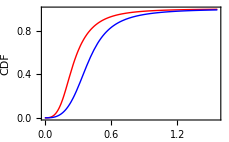

```mathematica
Block[{p1∞,p2∞,d},
p1∞=p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,∞},{0.1,1.}];
p2∞=p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,∞},{1.,∞}];
d=Max[duration[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0.1,1.}],duration[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{1.,∞}]];
PrintTemporary[Dynamic[t]];
Plot[{
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{0.1,1.}]/(p1∞),
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{1.,∞}]/(p2∞)
},{t,0,d},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","CDF"},PlotLegends->Placed[{Style["100 MeV - 1 GeV",FontSize->10],Style["1 GeV - 300 GeV",FontSize->10]},{0.7,0.25}],LabelStyle->Directive[FontSize->10],ImageSize->230.1799598
]
]
```

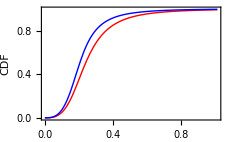

```mathematica
Block[{p1∞,p2∞,d},
p1∞=p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,∞},{0.1,1.}];
p2∞=p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,∞},{1.,∞}];
d=Max[duration[defaultUniverse[],defaultBurst[],defaultObserver[],{0.1,1.}],duration[defaultUniverse[],defaultBurst[],defaultObserver[],{1.,∞}]];
PrintTemporary[Dynamic[t]];
Plot[{
p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,t},{0.1,1.}]/(p1∞),
p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,t},{1.,∞}]/(p2∞)
},{t,0,d},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","CDF"},PlotLegends->Placed[{Style["100 MeV - 1 GeV",FontSize->10],Style["1 GeV - 300 GeV",FontSize->10]},{0.7,0.25}],LabelStyle->Directive[FontSize->10],ImageSize->230.1799598
]
]
```

Presentation

```mathematica
PrintTemporary[Dynamic[t]];
Plot[{
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{0.1,1.}]/(p1∞),
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{1.,∞}]/(p2∞)
},{t,0,1},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->{{True,False},{True,False}},FrameLabel->{"Time, normalized","Photons Fraction"},FrameStyle->Gray,PlotLegends->Placed[{Style["100 MeV - 1 GeV",Red],Style["1 GeV - 300 GeV",Blue]},{0.7,0.25}],ImageSize->225
]
```

-Graphics-

#### Stretching Factors Histogram

```mathematica
κObserved={
{Text["090902B"],{0.363408,0.893437}},
{Text["090510"],{0.428137,1.60485}},
{Text["080916C"],{0.66529,3.31569}},
{Text["090926A"],{1.98759,6.61486}}
};
```

```mathematica
errorBar[{min_,max_},y_,height_,{label_,x_}]:=Graphics[{Black,Line[{{min,y},{max,y}}],Line[{{min,y-height},{min,y+height}}],Line[{{max,y-height},{max,y+height}}],{Black,Inset[label,{x,y},{Right,Bottom}]}}];
```

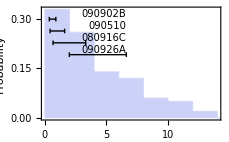

```mathematica
Block[{κ2,top},
κ2=Max[Transpose[Transpose[κObserved][[2]]][[2]]];
Show[
Histogram[mcDataIA[[All,-1]],Automatic,"Probability",PlotRangePadding->0,Frame->{{True,False},{True,False}},FrameLabel->{Style["Stretching Factor",FontSize->10],Style["Probability",FontSize->10]},PlotRange->{{0.,14},All}],
Table[errorBar[κObserved[[it]][[2]],0.30/0.25(0.25-0.03(it-1)),0.007,{Style[κObserved[[it]][[1]],FontSize->10],κ2}],{it,1,Length[κObserved]}],Axes->False,ImageSize->230.1799598
]
]
```

#### Stretching Factors CDF

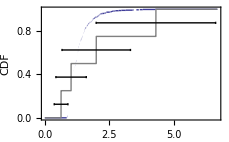

```mathematica
Block[{it,κ2},
κ2=Max[Transpose[Transpose[κObserved][[2]]][[2]]];
Show[
Plot[CDF[EmpiricalDistribution[mcData],κi],{κi,0.,1.01κ2},FrameLabel->{"Stretching Factor","CDF"},PlotRange->{{0,1.01κ2},All},Frame->{{True,False},{True,False}}],
Plot[CDF[EmpiricalDistribution[Table[Mean[value[[2]]],{value,κObserved}]],κi],{κi,0.,1.01κ2},PlotStyle->Gray],
Table[errorBar[κObserved[[it]][[2]],(2it-1)/(2Length[κObserved]),0.01,{"",κObserved[[it]][[2]][[1]]}],{it,1,Length[κObserved]}],Axes->False,ImageSize->230.1799598
]
]
```

```mathematica
Binomial[35,3] 0.072^3(1-0.072)^(35-3)
```

0.223585

#### Very High Energy Bursts Fraction

```mathematica
PrintTemporary[Dynamic[z]];
Timing[burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞}]]
```

{3321.83545,0.0720929}

```mathematica
PrintTemporary[Dynamic[z]];
Timing[burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst500[],defaultDetectorArea[],{0.1,1.,∞}]]
```

{3738.33563,0.010223}